```mathematica
(*1980*)

(*differences Y Vector*)
Data=Import["G:\\.shortcut-targets-by-id\\17WrugWUn3l1ON6QYmzE0UD-ifioHGbb0\\Priscila\\Research\\USMA\\New Approach\\COOLF1MathematicaReads.xlsx"];
```

```mathematica
(*the whole Y Vec*)
YVec=Data[[1,All,1]];
n=Length[YVec];

ΔYVec=Data[[1,All,2]];
nΔYVec=Length[ΔYVec];
```

```mathematica
(*fitting to 70% of the data*)
n90=Floor[nΔYVec (0.8)]
```

67

```mathematica
(*Covariates*)


(*Yield Curve*)
X1Vec=Data[[1,All,3]];

(*Norfarm Jobs*)
X2Vec=Data[[1,All,4]];

(*Federal Funds*)
X3Vec=Data[[1,All,5]];

(*Mortgage Rate*)
X4Vec=Data[[1,All,6]];

(*Personal Consumption Expeditures*)
X5Vec=Data[[1,All,7]];

(*Industrial Production*)
X6Vec=Data[[1,All,8]];

(*Consumer Price Index*)
X7Vec=Data[[1,All,9]];

(*Crude Oil Prices*)
X8Vec=Data[[1,All,10]];

(*NASDAQ Composite Index*)
X9Vec=Data[[1,All,11]];

(*Capacity Utilization*)
X10Vec=Data[[1,All,12]];
```

Part::partw: Part 12 of {{0.249077,0.,0.99,4559.,1519.,1519.,0.16524,1.,0.,0.,«1»},{0.0893193,-0.159757,0.99,4572.,1523.,1523.,0.0505581,1.,1.,0.,«1»},{0.299382,0.210063,0.99,4358.,1452.,1772.,0.130854,1.,2.,5.,«1»},{0.378311,0.078929,0.99,4119.,1372.,1980.,0.0881924,1.,3.,10.,«1»},«3»,{0.713062,0.14455,0.99,2350.,783.,3801.,0.157088,0.85222,7.,50.,«1»},{0.764528,0.0514665,0.99,2350.,783.,3785.,0.185185,0.955363,8.,50.,«1»},{0.742625,-0.0219038,0.99,2350.,783.,3794.,0.172414,0.90734,9.,50.,«1»},«74»} does not exist.

```mathematica
(*Plot Y - Observed data*)
```

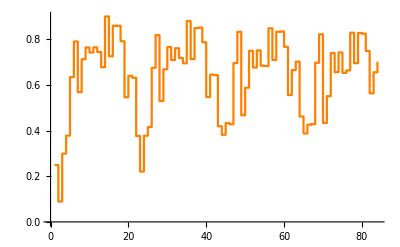

```mathematica
x=Table[i,{i,1,n}];
dataPlot=Transpose[{x,YVec}];
YObserved=ListPlot[dataPlot,InterpolationOrder->0, Joined->True,PlotRange->All,PlotStyle->Orange]
```

```mathematica
(*Linear Regression - Normal Distribution*)
L=1/((2 π σ^2)^(n90/2))Exp[-1/(2 σ^2) (∑_(i=2)^n90 ((ΔYVec[[i]]-(β0+β1 YVec[[i-1]]+β2 X1[[i-1]]+β3 X2[[i-1]]+β4 X3[[i-1]]+β5 X4[[i-1]]+β6 X5[[i-1]]+β7 Errors2[[i-1]]+β8 X1[[i]]+β9 X2[[i]]+β10 X3[[i]]+β11 X4[[i]]+β12 X5[[i]]))/.{X1->X3Vec,X2->X6Vec,X3->X4Vec,X4->X2Vec,X5->X8Vec})^2)];
LnL=Log[L];


Dβ0=Simplify[D[LnL,β0]];
Dβ1=Simplify[D[LnL,β1]];
Dβ2=Simplify[D[LnL,β2]];
Dβ3=Simplify[D[LnL,β3]];
Dβ4=Simplify[D[LnL,β4]];
Dβ5=Simplify[D[LnL,β5]];
Dβ6=Simplify[D[LnL,β6]];
Dβ7=Simplify[D[LnL,β7]];
Dβ8=Simplify[D[LnL,β8]];
Dβ9=Simplify[D[LnL,β9]];
Dβ10=Simplify[D[LnL,β10]];
Dβ11=Simplify[D[LnL,β11]];
Dβ12=Simplify[D[LnL,β12]];
Dσ=Simplify[D[LnL,σ]];

Rules=FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ5},{0==Dβ6},{0==Dβ7},{0==Dβ8},{0==Dβ9},{0==Dβ10},{0==Dβ11},{0==Dβ12},{0==Dσ}},{{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β5,0.1},{β6,0.1},{β7,0.1},{β8,0.1},{β9,0.1},{β10,0.1},{β11,0.1},{β12,0.1},{σ,0.1}},MaxIterations->1000]//Quiet
```

Part::partd: Part specification X1⟦1⟧ is longer than depth of object.

Part::partd: Part specification X2⟦1⟧ is longer than depth of object.

Part::partd: Part specification X3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindRoot::nlnum: The function value {6600. (1369.66+0.00151515 Errors2⟦1⟧+0.00151515 Errors2⟦2⟧+0.00151515 Errors2⟦3⟧+0.00151515 Errors2⟦4⟧+0.00151515 Errors2⟦5⟧+0.00151515 Errors2⟦6⟧+0.00151515 Errors2⟦7⟧+0.00151515 Errors2⟦8⟧+0.00151515 Errors2⟦9⟧+«57»),-100. (-56544.9-0.0249077 Errors2⟦1⟧-0.00893193 Errors2⟦2⟧-0.0299382 Errors2⟦3⟧-0.0378311 Errors2⟦4⟧-0.0634394 Errors2⟦5⟧-0.0790827 Errors2⟦6⟧-0.0568512 Errors2⟦7⟧-0.0713062 Errors2⟦8⟧-0.0764528 Errors2⟦9⟧+«57»),«8»,«4»} is not a list of numbers with dimensions {14} at {β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,«4»} = {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,«4»}.

FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ5},{0==Dβ6},{0==Dβ7},{0==Dβ8},{0==Dβ9},{0==Dβ10},{0==Dβ11},{0==Dβ12},{0==Dσ}},{{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β5,0.1},{β6,0.1},{β7,0.1},{β8,0.1},{β9,0.1},{β10,0.1},{β11,0.1},{β12,0.1},{σ,0.1}},MaxIterations→1000]

```mathematica
(*Prediction*)
LR=β0+β1 YVec[[i-1]]+β2 X1[[i-1]]+β3 X2[[i-1]]+β4 X3[[i-1]]+β5 X4[[i-1]]+β6 X5[[i-1]]+β7 Errors2[[i-1]]+β8 X1[[i]]+β9 X2[[i]]+β10 X3[[i]]+β11 X4[[i]]+β12 X5[[i]];
LR=LR/.Rules; 

YFitList=.
YFitList={YVec[[1]]};
For[k=2,k<=nΔYVec,
AppendTo[YFitList,LR/.{X1->X3Vec,X2->X6Vec,X3->X4Vec,X4->X2Vec,X5->X8Vec,i->k}]//Quiet;
k=k+1;
];
YFitList;
```

Part::pkspec1: The expression -1+i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindRoot::nlnum: The function value {6600. (1369.66+0.00151515 Errors2⟦1⟧+0.00151515 Errors2⟦2⟧+0.00151515 Errors2⟦3⟧+0.00151515 Errors2⟦4⟧+0.00151515 Errors2⟦5⟧+0.00151515 Errors2⟦6⟧+0.00151515 Errors2⟦7⟧+0.00151515 Errors2⟦8⟧+0.00151515 Errors2⟦9⟧+«57»),-100. (-56544.9-0.0249077 Errors2⟦1⟧-0.00893193 Errors2⟦2⟧-0.0299382 Errors2⟦3⟧-0.0378311 Errors2⟦4⟧-0.0634394 Errors2⟦5⟧-0.0790827 Errors2⟦6⟧-0.0568512 Errors2⟦7⟧-0.0713062 Errors2⟦8⟧-0.0764528 Errors2⟦9⟧+«57»),«8»,«4»} is not a list of numbers with dimensions {14} at {β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,«4»} = {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,«4»}.

ReplaceAll::reps: {FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ5},{0==Dβ6},{0==Dβ7},{0==Dβ8},{0==Dβ9},«4»},{{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β5,0.1},{β6,0.1},{β7,0.1},{β8,0.1},{β9,0.1},«4»},MaxIterations→1000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {6600. (1369.66+0.00151515 Errors2⟦1⟧+0.00151515 Errors2⟦2⟧+0.00151515 Errors2⟦3⟧+0.00151515 Errors2⟦4⟧+0.00151515 Errors2⟦5⟧+0.00151515 Errors2⟦6⟧+0.00151515 Errors2⟦7⟧+0.00151515 Errors2⟦8⟧+0.00151515 Errors2⟦9⟧+«57»),-100. (-56544.9-0.0249077 Errors2⟦1⟧-0.00893193 Errors2⟦2⟧-0.0299382 Errors2⟦3⟧-0.0378311 Errors2⟦4⟧-0.0634394 Errors2⟦5⟧-0.0790827 Errors2⟦6⟧-0.0568512 Errors2⟦7⟧-0.0713062 Errors2⟦8⟧-0.0764528 Errors2⟦9⟧+«57»),«8»,«4»} is not a list of numbers with dimensions {14} at {β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,«4»} = {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,«4»}.

ReplaceAll::reps: {FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ5},{0==Dβ6},{0==Dβ7},{0==Dβ8},{0==Dβ9},«4»},{{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β5,0.1},{β6,0.1},{β7,0.1},{β8,0.1},{β9,0.1},«4»},MaxIterations→1000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {6600. (1369.66+0.00151515 Errors2⟦1⟧+0.00151515 Errors2⟦2⟧+0.00151515 Errors2⟦3⟧+0.00151515 Errors2⟦4⟧+0.00151515 Errors2⟦5⟧+0.00151515 Errors2⟦6⟧+0.00151515 Errors2⟦7⟧+0.00151515 Errors2⟦8⟧+0.00151515 Errors2⟦9⟧+«57»),-100. (-56544.9-0.0249077 Errors2⟦1⟧-0.00893193 Errors2⟦2⟧-0.0299382 Errors2⟦3⟧-0.0378311 Errors2⟦4⟧-0.0634394 Errors2⟦5⟧-0.0790827 Errors2⟦6⟧-0.0568512 Errors2⟦7⟧-0.0713062 Errors2⟦8⟧-0.0764528 Errors2⟦9⟧+«57»),«8»,«4»} is not a list of numbers with dimensions {14} at {β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,«4»} = {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,«4»}.

ReplaceAll::reps: {FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ5},{0==Dβ6},{0==Dβ7},{0==Dβ8},{0==Dβ9},«4»},{{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β5,0.1},{β6,0.1},{β7,0.1},{β8,0.1},{β9,0.1},«4»},MaxIterations→1000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {6600. (1369.66+0.00151515 Errors2⟦1⟧+0.00151515 Errors2⟦2⟧+0.00151515 Errors2⟦3⟧+0.00151515 Errors2⟦4⟧+0.00151515 Errors2⟦5⟧+0.00151515 Errors2⟦6⟧+0.00151515 Errors2⟦7⟧+0.00151515 Errors2⟦8⟧+0.00151515 Errors2⟦9⟧+«57»),-100. (-56544.9-0.0249077 Errors2⟦1⟧-0.00893193 Errors2⟦2⟧-0.0299382 Errors2⟦3⟧-0.0378311 Errors2⟦4⟧-0.0634394 Errors2⟦5⟧-0.0790827 Errors2⟦6⟧-0.0568512 Errors2⟦7⟧-0.0713062 Errors2⟦8⟧-0.0764528 Errors2⟦9⟧+«57»),«8»,«4»} is not a list of numbers with dimensions {14} at {β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,«4»} = {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,«4»}.

ReplaceAll::reps: {FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ5},{0==Dβ6},{0==Dβ7},{0==Dβ8},{0==Dβ9},«4»},{{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β5,0.1},{β6,0.1},{β7,0.1},{β8,0.1},{β9,0.1},«4»},MaxIterations→1000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {6600. (1369.66+0.00151515 Errors2⟦1⟧+0.00151515 Errors2⟦2⟧+0.00151515 Errors2⟦3⟧+0.00151515 Errors2⟦4⟧+0.00151515 Errors2⟦5⟧+0.00151515 Errors2⟦6⟧+0.00151515 Errors2⟦7⟧+0.00151515 Errors2⟦8⟧+0.00151515 Errors2⟦9⟧+«57»),-100. (-56544.9-0.0249077 Errors2⟦1⟧-0.00893193 Errors2⟦2⟧-0.0299382 Errors2⟦3⟧-0.0378311 Errors2⟦4⟧-0.0634394 Errors2⟦5⟧-0.0790827 Errors2⟦6⟧-0.0568512 Errors2⟦7⟧-0.0713062 Errors2⟦8⟧-0.0764528 Errors2⟦9⟧+«57»),«8»,«4»} is not a list of numbers with dimensions {14} at {β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,«4»} = {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,«4»}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ5},{0==Dβ6},{0==Dβ7},{0==Dβ8},{0==Dβ9},«4»},{{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β5,0.1},{β6,0.1},{β7,0.1},{β8,0.1},{β9,0.1},«4»},MaxIterations→1000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

FindRoot::nlnum: The function value {6600. (1369.66+0.00151515 Errors2⟦1⟧+0.00151515 Errors2⟦2⟧+0.00151515 Errors2⟦3⟧+0.00151515 Errors2⟦4⟧+0.00151515 Errors2⟦5⟧+0.00151515 Errors2⟦6⟧+0.00151515 Errors2⟦7⟧+0.00151515 Errors2⟦8⟧+0.00151515 Errors2⟦9⟧+«57»),-100. (-56544.9-0.0249077 Errors2⟦1⟧-0.00893193 Errors2⟦2⟧-0.0299382 Errors2⟦3⟧-0.0378311 Errors2⟦4⟧-0.0634394 Errors2⟦5⟧-0.0790827 Errors2⟦6⟧-0.0568512 Errors2⟦7⟧-0.0713062 Errors2⟦8⟧-0.0764528 Errors2⟦9⟧+«57»),«8»,«4»} is not a list of numbers with dimensions {14} at {β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,«4»} = {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,«4»}.

ReplaceAll::reps: {FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ5},{0==Dβ6},{0==Dβ7},{0==Dβ8},{0==Dβ9},«4»},{{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β5,0.1},{β6,0.1},{β7,0.1},{β8,0.1},{β9,0.1},«4»},MaxIterations→1000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {6600. (1369.66+0.00151515 Errors2⟦1⟧+0.00151515 Errors2⟦2⟧+0.00151515 Errors2⟦3⟧+0.00151515 Errors2⟦4⟧+0.00151515 Errors2⟦5⟧+0.00151515 Errors2⟦6⟧+0.00151515 Errors2⟦7⟧+0.00151515 Errors2⟦8⟧+0.00151515 Errors2⟦9⟧+«57»),-100. (-56544.9-0.0249077 Errors2⟦1⟧-0.00893193 Errors2⟦2⟧-0.0299382 Errors2⟦3⟧-0.0378311 Errors2⟦4⟧-0.0634394 Errors2⟦5⟧-0.0790827 Errors2⟦6⟧-0.0568512 Errors2⟦7⟧-0.0713062 Errors2⟦8⟧-0.0764528 Errors2⟦9⟧+«57»),«8»,«4»} is not a list of numbers with dimensions {14} at {β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,«4»} = {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,«4»}.

ReplaceAll::reps: {FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ5},{0==Dβ6},{0==Dβ7},{0==Dβ8},{0==Dβ9},«4»},{{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β5,0.1},{β6,0.1},{β7,0.1},{β8,0.1},{β9,0.1},«4»},MaxIterations→1000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {6600. (1369.66+0.00151515 Errors2⟦1⟧+0.00151515 Errors2⟦2⟧+0.00151515 Errors2⟦3⟧+0.00151515 Errors2⟦4⟧+0.00151515 Errors2⟦5⟧+0.00151515 Errors2⟦6⟧+0.00151515 Errors2⟦7⟧+0.00151515 Errors2⟦8⟧+0.00151515 Errors2⟦9⟧+«57»),-100. (-56544.9-0.0249077 Errors2⟦1⟧-0.00893193 Errors2⟦2⟧-0.0299382 Errors2⟦3⟧-0.0378311 Errors2⟦4⟧-0.0634394 Errors2⟦5⟧-0.0790827 Errors2⟦6⟧-0.0568512 Errors2⟦7⟧-0.0713062 Errors2⟦8⟧-0.0764528 Errors2⟦9⟧+«57»),«8»,«4»} is not a list of numbers with dimensions {14} at {β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,«4»} = {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,«4»}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ5},{0==Dβ6},{0==Dβ7},{0==Dβ8},{0==Dβ9},«4»},{{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β5,0.1},{β6,0.1},{β7,0.1},{β8,0.1},{β9,0.1},«4»},MaxIterations→1000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
YFitCumulative=.
YFitCumulative={YFitList[[1]]};
For[k=1,k<nΔYVec,
AppendTo[YFitCumulative,(YFitCumulative[[k]]+YFitList[[k+1]])]//Quiet;
k=k+1;
];
YFitCumulative
```

{1.,1.00288,1.00613,1.00855,1.01155,1.01397,1.01498,1.01582,1.01818,1.02034,1.02105,1.02116,1.0219,1.02301,1.02591,1.02467,1.02082,1.01836,1.0155,1.01488,1.01726,1.0194,1.02198,1.02478,1.02546,1.02598,1.02698,1.02743,1.02833,1.02935,1.02925,1.02896,1.02858,1.02715,1.02389,1.02097,1.01905,1.01776,1.0167,1.01409,1.01164,1.00974,1.00746,1.00477,1.00256,1.00056,0.999826,0.999583,1.00011,1.00233,1.00554,1.00829,1.01173,1.01569,1.01894,1.02369,1.02845,1.03405,1.03967,1.04549}

```mathematica
IndexCount = Table[index,{index,1,nΔYVec}];
Transpose[{YFitCumulative,IndexCount}]
```

{{1.,1},{1.00288,2},{1.00613,3},{1.00855,4},{1.01155,5},{1.01397,6},{1.01498,7},{1.01582,8},{1.01818,9},{1.02034,10},{1.02105,11},{1.02116,12},{1.0219,13},{1.02301,14},{1.02591,15},{1.02467,16},{1.02082,17},{1.01836,18},{1.0155,19},{1.01488,20},{1.01726,21},{1.0194,22},{1.02198,23},{1.02478,24},{1.02546,25},{1.02598,26},{1.02698,27},{1.02743,28},{1.02833,29},{1.02935,30},{1.02925,31},{1.02896,32},{1.02858,33},{1.02715,34},{1.02389,35},{1.02097,36},{1.01905,37},{1.01776,38},{1.0167,39},{1.01409,40},{1.01164,41},{1.00974,42},{1.00746,43},{1.00477,44},{1.00256,45},{1.00056,46},{0.999826,47},{0.999583,48},{1.00011,49},{1.00233,50},{1.00554,51},{1.00829,52},{1.01173,53},{1.01569,54},{1.01894,55},{1.02369,56},{1.02845,57},{1.03405,58},{1.03967,59},{1.04549,60}}

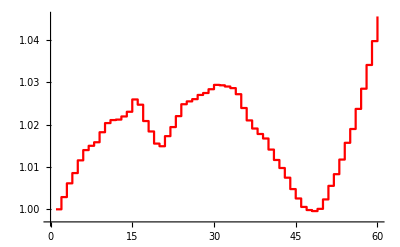

```mathematica
YPredictedPlot=ListPlot[(YFitCumulative),InterpolationOrder->0, Joined->True,PlotStyle->Red,PlotRange->All]
```

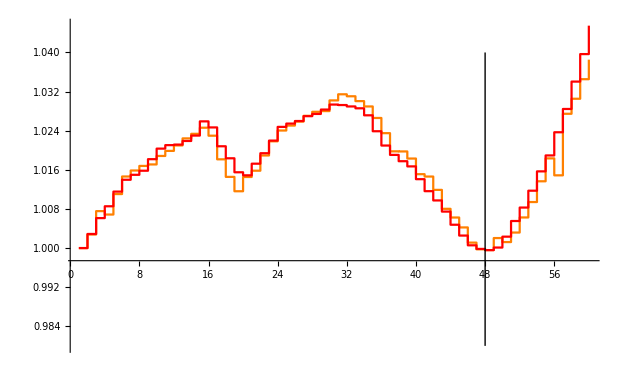

```mathematica
(*Comparing Y observed vs Y predicted with multiple linear regression*)

A=Show[{YObserved,YPredictedPlot},Graphics[{Black, Line[{{n90,0.98},{n90,1.04}}]}],PlotRange->All]
```

```mathematica
(*Measure of the quality of the fit *)


(*numer of parameters in the model*)
p=13;

(*Prediction of Y using X*)
SSE=∑_(i=1)^nΔYVec (YVec[[i]]-YFitCumulative[[i]])^2;
```

```mathematica
(*RMSE*)
```

```mathematica
RMSE=Sqrt[1/(n-p)∑_(i=1)^nΔYVec (YVec[[i]]-YFitCumulative[[i]])^2]
```

0.00254236

```mathematica
(*PMSE*)
PMSE=Sqrt[1/(n-n90+1)∑_(i=n90+1)^nΔYVec (YVec[[i]]-YFitCumulative[[i]])^2]
```

0.00382455

```mathematica
(*Correlation Coefficient*)
```

```mathematica
(*prediction of Y if X is ignored*)
```

```mathematica
SSY=∑_(i=1)^nΔYVec (ΔYVec[[i]]-Mean[ΔYVec])^2;
```

```mathematica
(*p is the number of independent variables in the model (excluding the constant term)*)
```

```mathematica
r2Adj=1-(1-((SSY-SSE)/SSY))(n-1)/(n-p-1)
```

0.231272

```mathematica
(*Residuals*)
```

```mathematica
Residuals={};
For[k=1,k<=nΔYVec,
AppendTo[Residuals,YVec[[k]]-YFitCumulative[[k]]]//Quiet;
k=k+1;
];
Residuals
```

{0.,-0.000102719,0.00142689,-0.00169064,-0.000502401,0.000669249,0.000883622,0.000982639,-0.00107591,-0.00150019,-0.00117671,-0.000174369,0.000528973,0.000357531,-0.00129761,-0.00169174,-0.00266846,-0.00380263,-0.00388084,-0.000339711,-0.00143709,-0.000458073,-0.000146619,-0.00074402,-0.000404008,-0.000119743,0.0000712201,0.000437098,-0.000311108,0.000850753,0.00219902,0.00208082,0.00146947,0.00181031,0.00271545,0.00253105,0.000729857,0.00199691,0.00160503,0.00102185,0.00298973,0.00216018,0.000566842,0.00147651,0.00166393,0.000549897,-0.0000738907,-2.22045×10^-16,0.00194171,-0.00110654,-0.00235994,-0.00202586,-0.00232036,-0.00202824,-0.000601913,-0.00881064,-0.000983535,-0.00350833,-0.00513489,-0.00695376}

```mathematica
Transpose[{Residuals,IndexCount}]
```

{{0.,1},{-0.000102719,2},{0.00142689,3},{-0.00169064,4},{-0.000502401,5},{0.000669249,6},{0.000883622,7},{0.000982639,8},{-0.00107591,9},{-0.00150019,10},{-0.00117671,11},{-0.000174369,12},{0.000528973,13},{0.000357531,14},{-0.00129761,15},{-0.00169174,16},{-0.00266846,17},{-0.00380263,18},{-0.00388084,19},{-0.000339711,20},{-0.00143709,21},{-0.000458073,22},{-0.000146619,23},{-0.00074402,24},{-0.000404008,25},{-0.000119743,26},{0.0000712201,27},{0.000437098,28},{-0.000311108,29},{0.000850753,30},{0.00219902,31},{0.00208082,32},{0.00146947,33},{0.00181031,34},{0.00271545,35},{0.00253105,36},{0.000729857,37},{0.00199691,38},{0.00160503,39},{0.00102185,40},{0.00298973,41},{0.00216018,42},{0.000566842,43},{0.00147651,44},{0.00166393,45},{0.000549897,46},{-0.0000738907,47},{-2.22045×10^-16,48},{0.00194171,49},{-0.00110654,50},{-0.00235994,51},{-0.00202586,52},{-0.00232036,53},{-0.00202824,54},{-0.000601913,55},{-0.00881064,56},{-0.000983535,57},{-0.00350833,58},{-0.00513489,59},{-0.00695376,60}}

```mathematica
(*Cumulative Residuals *)
```

```mathematica
ResidualsCumulative=.
ResidualsCumulative={Residuals[[1]]};
For[k=1,k<nΔYVec,
AppendTo[ResidualsCumulative,(ResidualsCumulative[[k]]+Residuals[[k+1]])]//Quiet;
k=k+1;
];
ResidualsCumulative/Max[ResidualsCumulative]
```

{0.,-0.00847655,0.109272,-0.0302416,-0.0717004,-0.0164731,0.0564446,0.137533,0.0487476,-0.0750501,-0.172154,-0.186543,-0.142892,-0.113388,-0.220468,-0.360073,-0.580278,-0.894076,-1.21433,-1.24236,-1.36095,-1.39875,-1.41085,-1.47225,-1.50559,-1.51547,-1.50959,-1.47352,-1.4992,-1.42899,-1.24753,-1.07581,-0.95455,-0.805161,-0.581078,-0.372212,-0.311983,-0.147195,-0.0147457,0.0695788,0.316296,0.494557,0.541333,0.663177,0.800487,0.845865,0.839767,0.839767,1.,0.908687,0.713941,0.546764,0.355285,0.187913,0.138242,-0.588824,-0.669987,-0.959499,-1.38324,-1.95707}

```mathematica
(*Standardized Residuals *)
StandardResiduals={};
SumX=∑_(i=1)^nΔYVec (X1[[i]]-Mean[X1])^2/.{X1->X3Vec}//N;//Quiet
For[k=1,k<=nΔYVec,
AppendTo[StandardResiduals,((YVec[[k]]-YFitCumulative[[k]])/(Sqrt[(SSE/(n-2))]Sqrt[1-(1/nΔYVec+(X1[[k]]-Mean[X1])^2/SumX)]))/.{X1->X3Vec}]//Quiet;
k=k+1;
];
Transpose[{StandardResiduals,IndexCount}]
```

{{0.,1},{-0.0454272,2},{0.631034,3},{-0.747677,4},{-0.222184,5},{0.295972,6},{0.390778,7},{0.434568,8},{-0.475818,9},{-0.663452,10},{-0.520397,11},{-0.0771139,12},{0.233221,13},{0.157541,14},{-0.580305,15},{-0.746044,16},{-1.19537,17},{-1.73336,18},{-1.77738,19},{-0.151,20},{-0.635368,21},{-0.202484,22},{-0.0658801,23},{-0.335672,24},{-0.178221,25},{-0.0527712,26},{0.0314158,27},{0.192723,28},{-0.137423,29},{0.376794,30},{0.969955,31},{0.91689,32},{0.6475,33},{0.799087,34},{1.20066,35},{1.13188,36},{0.323091,37},{0.883216,38},{0.710933,39},{0.45173,40},{1.32106,41},{0.957432,42},{0.250245,43},{0.652537,44},{0.735791,45},{0.243093,46},{-0.0326231,47},{-9.80641×10^-14,48},{0.85567,49},{-0.48791,50},{-1.05327,51},{-0.90452,52},{-1.03332,53},{-0.907432,54},{-0.269586,55},{-4.03682,56},{-0.44735,57},{-1.58993,58},{-2.34621,59},{-3.17409,60}}

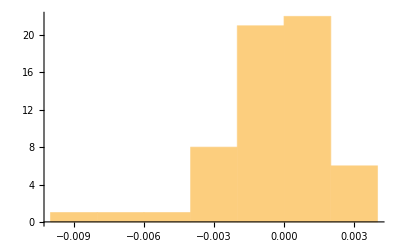

```mathematica
Histogram[Residuals]
```

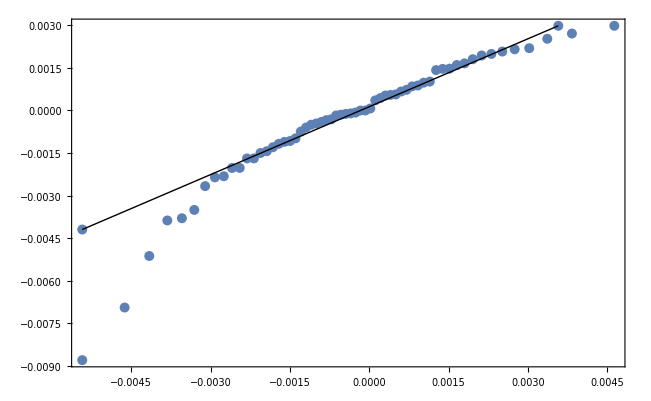

```mathematica
QuantilePlot[Residuals]
```

```mathematica
KolmogorovSmirnovTest[Residuals]
```

0.0504151

```mathematica
AndersonDarlingTest[Residuals]
```

0.00313625